# Approximate expressions for the escape energy

```mathematica
SetDirectory[NotebookDirectory[]]
```

E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new

Here we obtain approximate expressions for the escape energy using the data obtained from “EscapeEnergyData.nb”. The data are located in “E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData”. We try to fit the data to the expression ε(ρ_0)=a+b/ρ_0+c/ρ_0^2.

## Positive l

```mathematica
files=FileNames["*.mx",{"E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\PositiveL"}]
```

{E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b01EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b02EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b03EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b04EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\PositiveL\b05EscEdat.mx}

```mathematica
data=Import[#]&/@files;
```

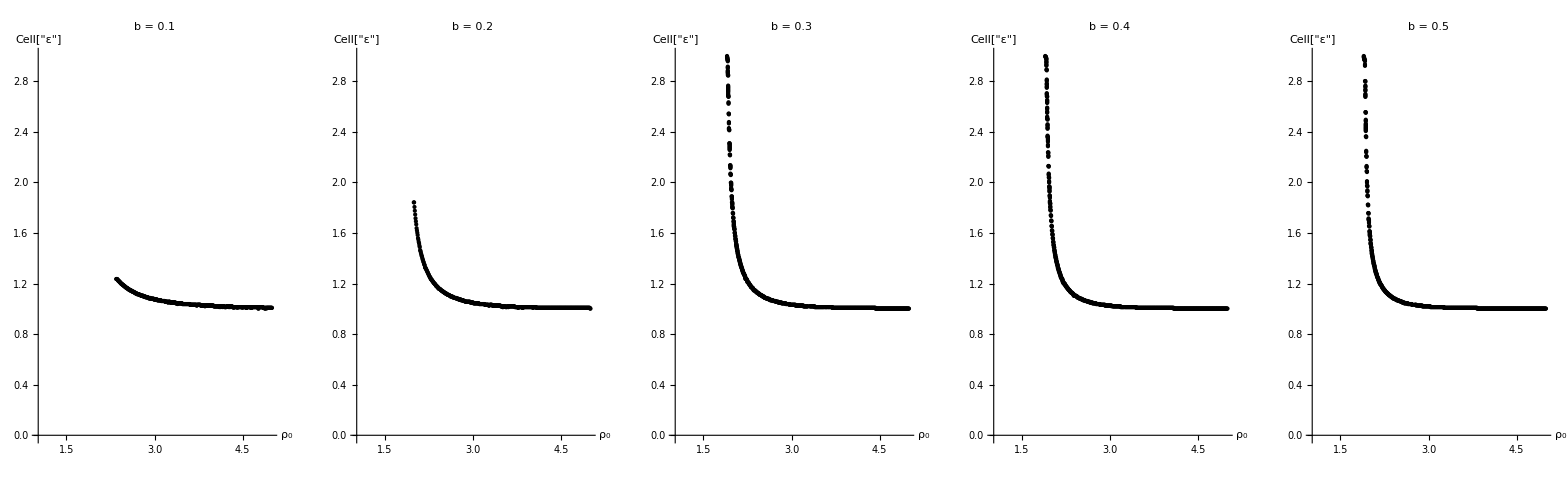

```mathematica
GraphicsRow[Table[ListPlot[data⟦i⟧,PlotRange->{{1,5},{0,3}},PlotStyle->{Black,PointSize[Small]},AxesLabel->{"ρ_0","Cell["ε",ExpressionUUID->"1f9a1c9e-ea09-41db-951b-ec84cca67e80"]"},LabelStyle->{FontSize->16},PlotLabel->"b = "<>ToString[i/10//N],ImageSize->600,AspectRatio->Automatic],{i,1,5}]]
```

```mathematica
dataPlot=Table[ListPlot[data⟦i⟧,PlotRange->{{1,5},{0,3}},PlotStyle->{Black,PointSize[Small]},AxesLabel->{"ρ_0","Cell["ε",ExpressionUUID->"0d5d9110-0168-4d6c-bdf8-486c77f7799f"]"},LabelStyle->{FontSize->16},PlotLabel->"b = "<>ToString[i/10//N],ImageSize->600,AspectRatio->Automatic],{i,1,5}];
```

```mathematica
plotColors={Red,Green,Blue,Yellow,Purple}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[0.5, 0, 0.5]}

```mathematica
eqn1=Table[Fit[data⟦i⟧,{1,1/x,1/x^2},x],{i,1,5}];
```

```mathematica
eqn1Plot=Table[Plot[eqn1⟦i⟧,{x,1,5},PlotRange->{{1,5},{0,3}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

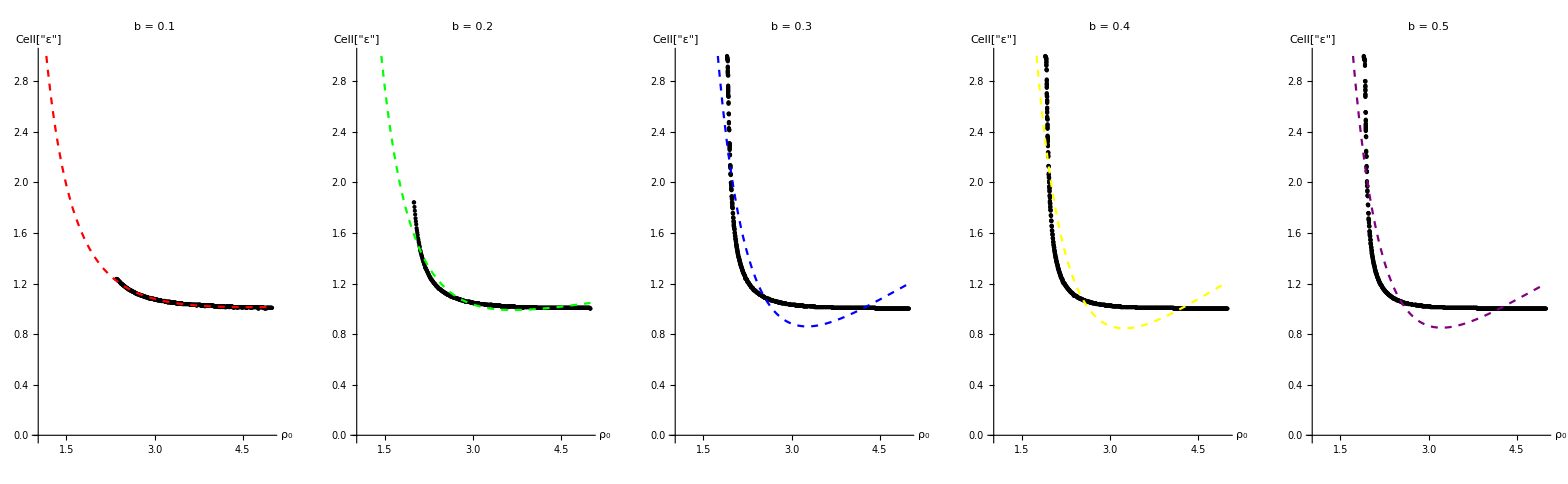

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqn1Plot⟦i⟧],{i,1,5}]]
```

```mathematica
For[i=1,i≤5,i++,
Export["escEplb0"<>ToString[i],Show[dataPlot⟦i⟧,eqn1Plot⟦i⟧]]
]
```

```mathematica
For[i=1,i≤5,i++,
Print["b = "<>ToString[i/10//N]<>": "eqn⟦i⟧]
]
```

b = 0.1:  (1.23458+4.74179/x^2-2.04749/x)

b = 0.2:  (1.81053+11.1806/x^2-6.05477/x)

b = 0.3:  (3.68224+30.1035/x^2-18.432/x)

b = 0.4:  (3.80872+31.1356/x^2-19.2097/x)

b = 0.5:  (3.62106+28.8071/x^2-17.8667/x)

We see from above that the fit is not accurate for positive l.

We have good reasons to believe that the escape energy for the case of positive l asymptotes to 1, i.e. ε_esc→ 1 as ρ_0→ ∞. We try to fit this set of data to the expression  ε_esc= 1+a ρ_0^-b.

```mathematica
eqn2=Table[1+a x^-b/.FindFit[data⟦i⟧,1+a x^-b,{a,b},x],{i,1,5}];
eqn2Plot=Table[Plot[eqn2⟦i⟧,{x,1,5},PlotRange->{{1,5},{0,3}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

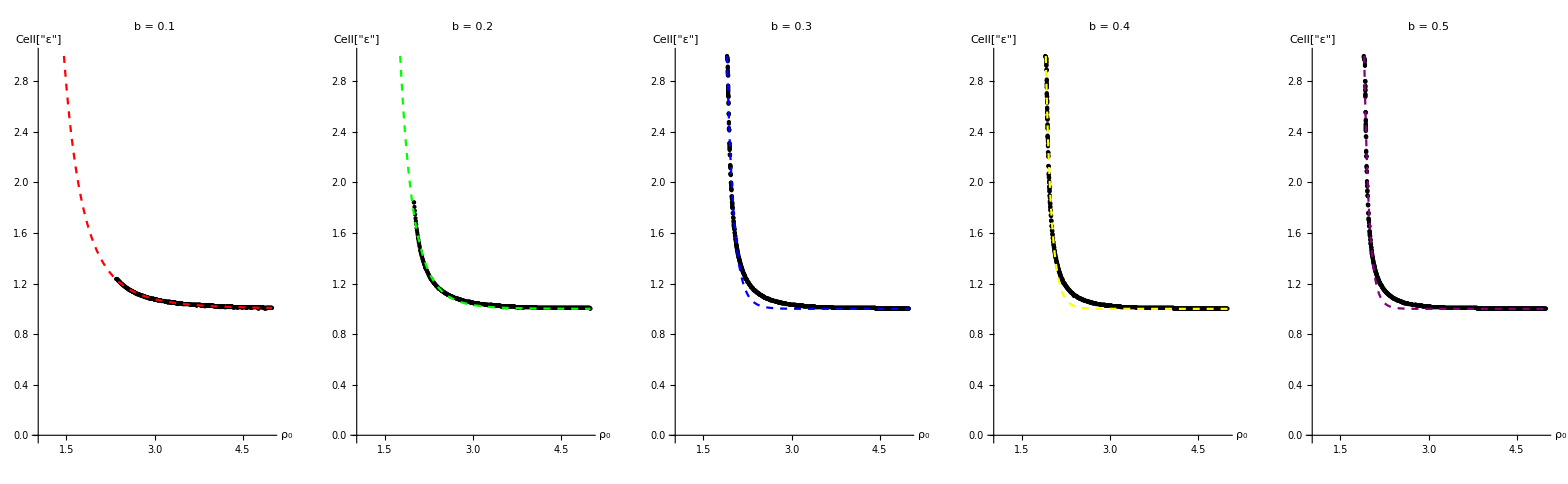

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqn2Plot⟦i⟧],{i,1,5}]]
```

```mathematica
For[i=1,i≤5,i++,
Print["b = "<>ToString[i/10//N]<>": "eqn2⟦i⟧]
]
```

b = 0.1:  (1+11.0022/x^4.51897)

b = 0.2:  (1+169.629/x^7.85412)

b = 0.3:  (1+108092./x^16.949)

b = 0.4:  (1+721077./x^19.8326)

b = 0.5:  (1+(4.36838×10^6)/x^22.6423)

We see that this is a better fit. Next we try to fit the set of data to the expression  ε_esc= Exp(a/ρ_0). With this form, we still have ε_esc→ 1 as ρ_0→ ∞.

```mathematica
eqn3=Table[Exp[a/x]/.FindFit[data⟦i⟧,Exp[a/x],{a},x],{i,1,5}];
eqn3Plot=Table[Plot[eqn3⟦i⟧,{x,1,5},PlotRange->{{1,5},{0,3}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

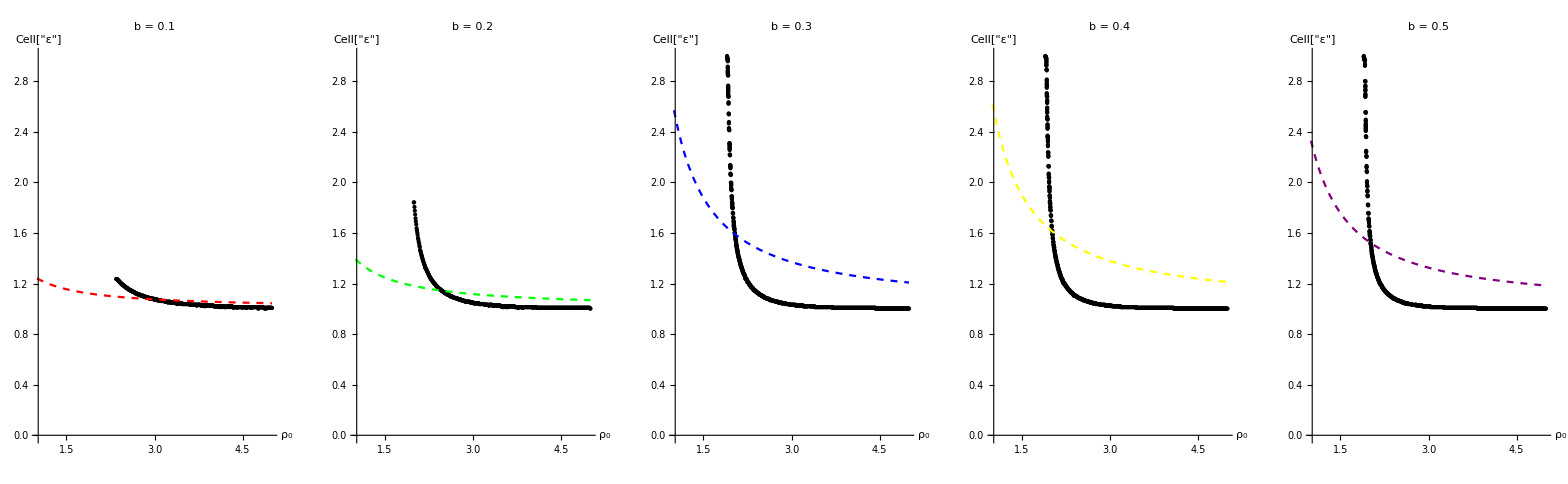

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqn3Plot⟦i⟧],{i,1,5}]]
```

Very bad fit lol

## Negative l

```mathematica
files=FileNames["*.mx",{"E:\\Joshua\\Documents\\Physics\\Mathematica notebooks\\Research\\WeakMagField2\\new\\EscapeEnergyData\\NegativeL"}]
```

{E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b01EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b02EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b03EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b04EscEdat.mx,E:\Joshua\Documents\Physics\Mathematica notebooks\Research\WeakMagField2\new\EscapeEnergyData\NegativeL\b05EscEdat.mx}

```mathematica
data=Import[#]&/@files;
```

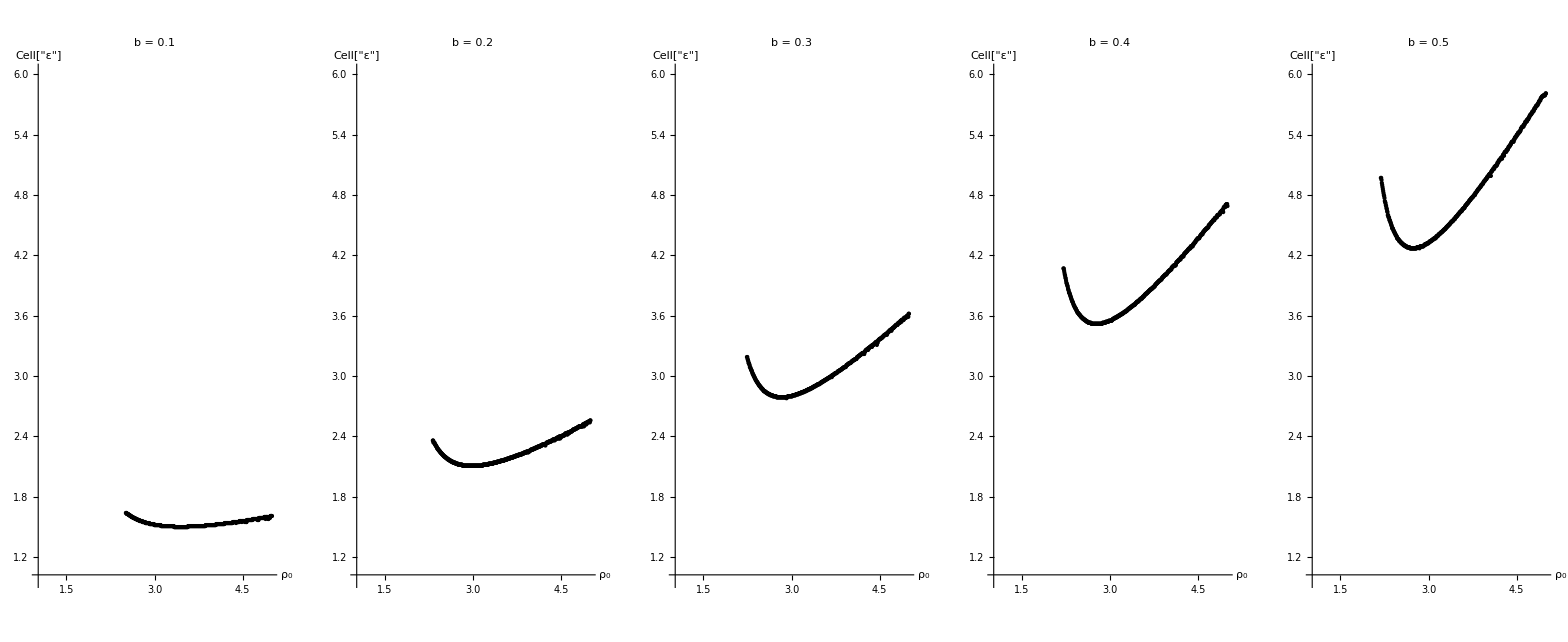

```mathematica
GraphicsRow[Table[ListPlot[data⟦i⟧,PlotRange->{{1,5},{1,6}},PlotStyle->{Black,PointSize[Small]},AxesLabel->{"ρ_0","Cell["ε",ExpressionUUID->"d68ab53d-5fd5-4fda-a48d-866e977a9459"]"},LabelStyle->{FontSize->16},PlotLabel->"b = "<>ToString[i/10//N],ImageSize->600,AspectRatio->1],{i,1,5}]]
```

```mathematica
dataPlot=Table[ListPlot[data⟦i⟧,PlotRange->{{1,5},{1,6}},PlotStyle->{Black,PointSize[Small]},AxesLabel->{"ρ_0","Cell["ε",ExpressionUUID->"c15653df-fc05-4c81-a186-bb306a6b9430"]"},LabelStyle->{FontSize->16},PlotLabel->"b = "<>ToString[i/10//N],ImageSize->600,AspectRatio->1],{i,1,5}];
```

```mathematica
plotColors={Red,Green,Blue,Yellow,Purple}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[0.5, 0, 0.5]}

```mathematica
eqn=Table[Fit[data⟦i⟧,{1,1/x,1/x^2},x],{i,1,5}];
```

```mathematica
eqnPlot=Table[Plot[eqn⟦i⟧,{x,1,5},PlotRange->{{1,5},{1,6}},PlotStyle->{Dashed,plotColors⟦i⟧}],{i,1,5}];
```

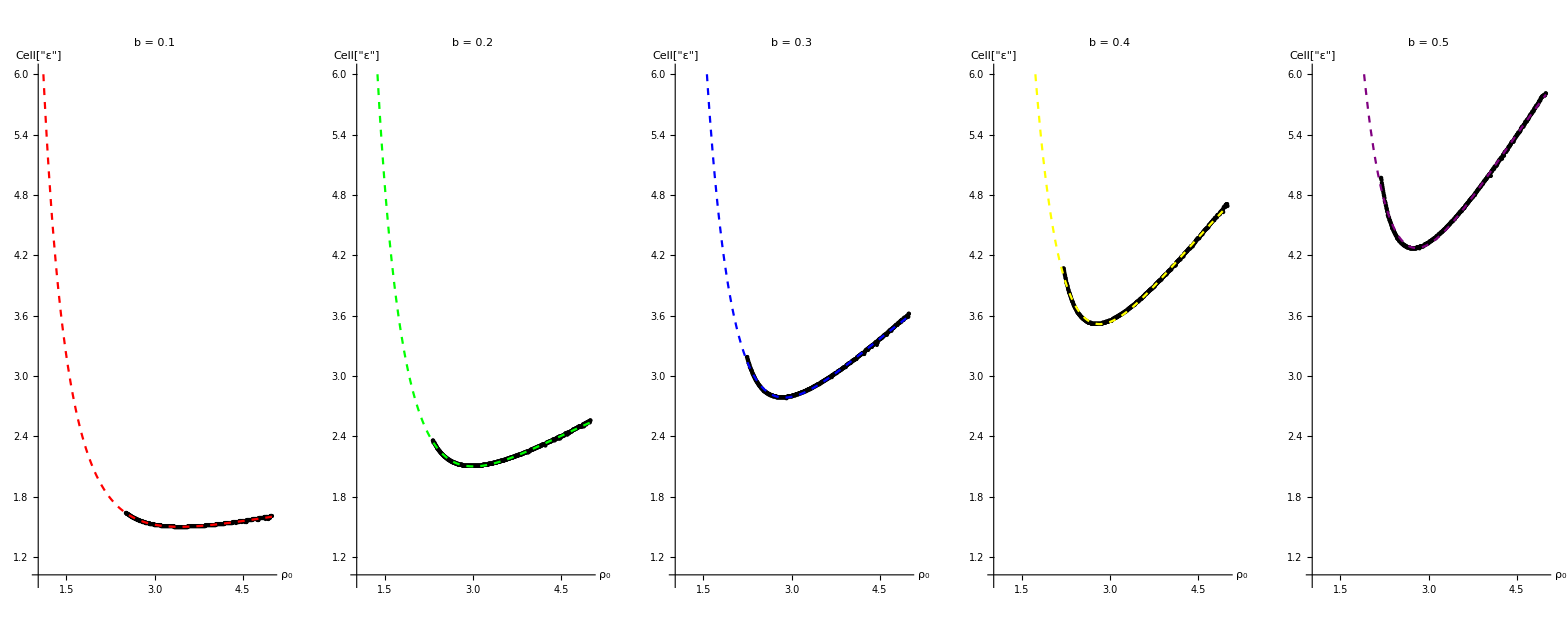

```mathematica
GraphicsRow[Table[Show[dataPlot⟦i⟧,eqnPlot⟦i⟧],{i,1,5}]]
```

```mathematica
For[i=1,i≤5,i++,
Print["b = "<>ToString[i/10//N]<>": "eqn⟦i⟧]
]
```

b = 0.1:  (2.52302+12.0311/x^2-7.00817/x)

b = 0.2:  (4.85533+24.8838/x^2-16.5521/x)

b = 0.3:  (7.27755+37.2119/x^2-25.8539/x)

b = 0.4:  (9.70931+49.4048/x^2-34.9811/x)

b = 0.5:  (12.124+61.3671/x^2-43.8987/x)

We can see from above that the fit is quite accurate for negative l.